```mathematica
daten={#[[2]],#[[1]]}&/@hedgeI;
d={{{0,0,0},{0,1,0}},{{1,0,0},{1,1,1}}};
n=Length[d]-1;(*Anzahl der Punkte - 1*)
p=3;(*Ordnung*)
m=n+1+p ;(*Anzahl der Knots - 1*)
(*Knot-Erzeugung*)
u=Join[Table[0,{i,p}],Table[i/(n+1-p),{i,0,n+1-p}],Table[1,{i,p}]];w=Table[ts[i],{i,5,8}];
```

```mathematica
ListPlot3D[Flatten[d,1]]
```

-Graphics3D-

```mathematica
P[t0_]:=Module[{ab,a,k,j=m,i,t=t0,u=u,d=d*w,p=p,n=n,m=m,w=w},
(*j Bestimmtung*)
If[t==0,j=1,
While[t<=u[[j]],j--]];
If[j<=p,j=p+1];

ab=Table[{0,0},{i,n+1}];

(*Berechnung*)
For[k=1,k≤p,k++,
For[i=j-p+k,i≤j,i++,
a=(t-u[[i]])/(u[[i+p+1-k]]-u[[i]]);
ab[[i]]=(1-a)ab[[i-1]]+a ab[[i]]+(d[[i]]-d[[i-1]])/(u[[i+p+1-k]]-u[[i]]);

d[[i]]=(1-a)d[[i-1]]+a d[[i]];
w[[i]]=(1-a)w[[i-1]]+a w[[i]];
];
];
Simplify[Append[d[[j]]/w[[j]],#[[2]]/#[[1]]&[ab[[j]]]]]
]
```

```mathematica
tt=Table[P[f[x,2]],{x,0,1,0.01}];
```

```mathematica
tt[[3]]
```

{(0.000799999 ts[1] ts[6]+6.40511×10^-7 ts[3] ts[7]+5.12×10^-10 ts[8])/(0.999199 ts[5]+0.000799999 ts[6]+6.40511×10^-7 ts[7]+5.12×10^-10 ts[8]),(-0.0114634 ts[5]+0.000799999 ts[2] ts[6]+6.40511×10^-7 ts[4] ts[7]+6.05469×10^-12 ts[8])/(0.999199 ts[5]+0.000799999 ts[6]+6.40511×10^-7 ts[7]+5.12×10^-10 ts[8]),(0.011491 ts[5]+0.999998 ts[2] ts[6]+0.00160192 ts[4] ts[7]+2.27051×10^-8 ts[8])/(0.999998 ts[1] ts[6]+0.00160192 ts[3] ts[7]+1.92×10^-6 ts[8])}

```mathematica
s[v0_]:=Module[{i,s=0,y,b,v=v0,tt=tt/.Table[ts[i]->v0[[i]],{i,8}],daten=daten,n=Length[tt],j},
For[i=2,i<Length[daten],i++,

(*j Bestimmtung*)
j=n;
While[daten[[i,1]]≤tt[[j,1]],j--];

b=tt[[j+1,1]]-tt[[j,1]];y=daten[[i,1]]-tt[[j,1]];
s+=(daten[[i,2]]-{tt[[j,2]],tt[[j+1,2]],tt[[j,3]],tt[[j+1,3]]}.{1-(3 y^2)/b^2+(2 y^3)/b^3,(3 y^2)/b^2-(2 y^3)/b^3,y-(2 y^2)/b+y^3/b^2,-y^2/b+y^3/b^2})^2;
];
s/Variance[Transpose[daten][[2]]]/Length[daten]]
```

```mathematica
n1=10;n2=10;min=10^10;pmin={};
For[i=0,i≤n1,i++,

For[j=0,j≤n1,j++,
Print[min];
For[k=0,k≤n2,k++,
For[l=0,l≤n2,l++,

t1=-2+6i/n1;
t2=-2+6j/n1;
t3=-0.05+0.1k/n2;
t4=-0.05+0.1l/n2;

st=s[{t1,t2,t3,t4,1,1,1,1}];
If[st<min,min=st;pmin={i,j,k,l}];

]]]]
```

```mathematica
pmin
```

{0,3,0,9}

```mathematica
t1=-2
t2=-2+6*3/n1;
t3=-0.05
t4=-0.05+0.1*9/n2;
```

23.8601

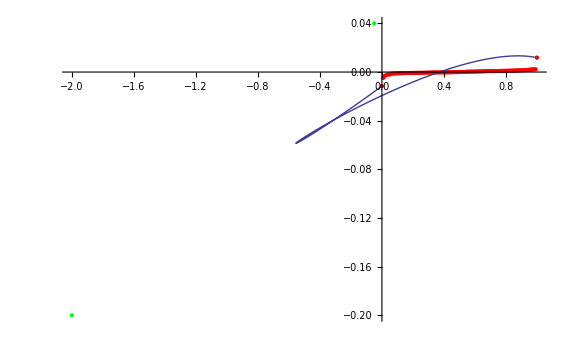

```mathematica
v={-2,-2+6*3/n1,-0.05,-0.05+0.1*9/n2,1,1,1,1};s[v]
Show[ListPlot[d/.Table[ts[i]->v[[i]],{i,8}],PlotStyle->Green],ListPlot[daten,PlotStyle->Red,PlotRange->All],ListPlot[Transpose[Transpose[tt][[1;;2]]]/.Table[ts[i]->v[[i]],{i,8}],Joined->True,PlotRange->All]]
```

```mathematica
f[x_,n_]:=Piecewise[{{(2x)^n/2,x≤0.5}},-(2-2x)^n/2+1];Plot[f[x,2],{x,0,1}];
```

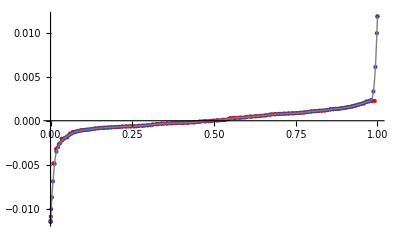

```mathematica
Show[ListPlot[d,Joined->False,PlotStyle->Red,PlotRange->All],ListPlot[tt,Joined->False,PlotRange->All],Plot[IP[x],{x,0,1},PlotStyle->Gray,PlotRange->All]]
```

```mathematica
IP[t0_]:=Module[{t=t0,tt=tt,j=Length[tt],m=ab,y},
(*j Bestimmtung*)
If[t==0,j=1,
While[t≤tt[[j,1]],j--]];
b=tt[[j+1,1]]-tt[[j,1]];y=t-tt[[j,1]];
{tt[[j,2]],tt[[j+1,2]],m[[j]],m[[j+1]]}.{1-(3 y^2)/b^2+(2 y^3)/b^3,(3 y^2)/b^2-(2 y^3)/b^3,y-(2 y^2)/b+y^3/b^2,-y^2/b+y^3/b^2}
]
```